```mathematica
(* Bifurcation kxx *)
Tb =7.771226149098018; (* From solution*)
s1x=Plot[(3.41479454240454*^28 ΔT-0.06689194487264087 √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2))/(1.85861773321361*^28-1.2689146717396477*^28 ΔT^2+1. ΔT √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2)),{ΔT,-7.771226149098018,-120.0},PlotRange->All];
s2x= Plot[(3.41479454240454*^28 ΔT+0.06689194487264087 √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2))/(1.85861773321361*^28-1.2689146717396477*^28 ΔT^2-1. ΔT √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2)),{ΔT,-7.771226149098018,-120.0}, PlotRange->All];
s3x=Plot[(-1.666676736466403*^34 ΔT-9.302686471020136*^33 Root[-1.666676736466403*^34 ΔT+1.731730866143749*^35 #1+1.5226090250626957*^36 #1^3&,1])/(1.8247577308539504*^35+1.5226090250626957*^36 Root[-1.666676736466403*^34 ΔT+1.731730866143749*^35 #1+1.5226090250626957*^36 #1^3&,1]^2),{ΔT,0,-120}, PlotRange->All, PlotStyle->Dashed];
```

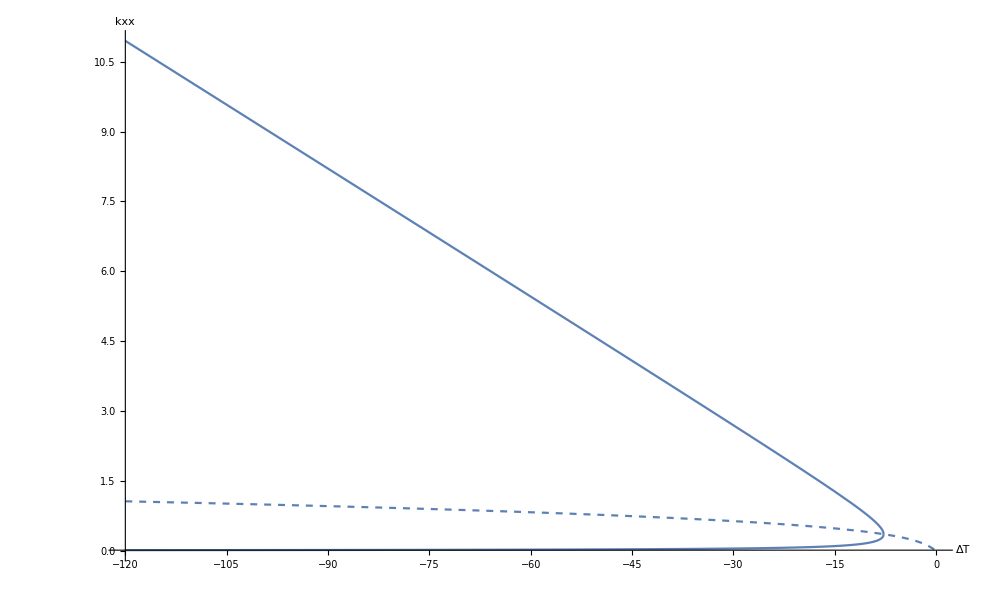

```mathematica
Show [s1x,s2x,s3x,AxesLabel->{"ΔT","kxx"}]
```

```mathematica
(* Bifurcation w out of plane disp at x-> a and y-> 0 *)
p1x= Plot[(0.0028125 (3.41479454240454*^28 ΔT-0.06689194487264087 √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2)))/(1.85861773321361*^28-1.2689146717396477*^28 ΔT^2+1. ΔT √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2)),{ΔT,-120,-Tb},PlotRange->All];
p2x= Plot[(0.0028125 (3.41479454240454*^28 ΔT+0.06689194487264087 √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2)))/(1.85861773321361*^28-1.2689146717396477*^28 ΔT^2-1. ΔT √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2)),{ΔT,-120,-Tb},PlotRange->All];
p3x= Plot[(0.0028125 (-1.666676736466403*^34 ΔT-9.302686471020136*^33 Root[-1.666676736466403*^34 ΔT+1.731730866143749*^35 #1+1.5226090250626957*^36 #1^3&,1]))/(1.8247577308539504*^35+1.5226090250626957*^36 Root[-1.666676736466403*^34 ΔT+1.731730866143749*^35 #1+1.5226090250626957*^36 #1^3&,1]^2),{ΔT,-120,0},PlotRange->All,PlotStyle->Dashed];
```

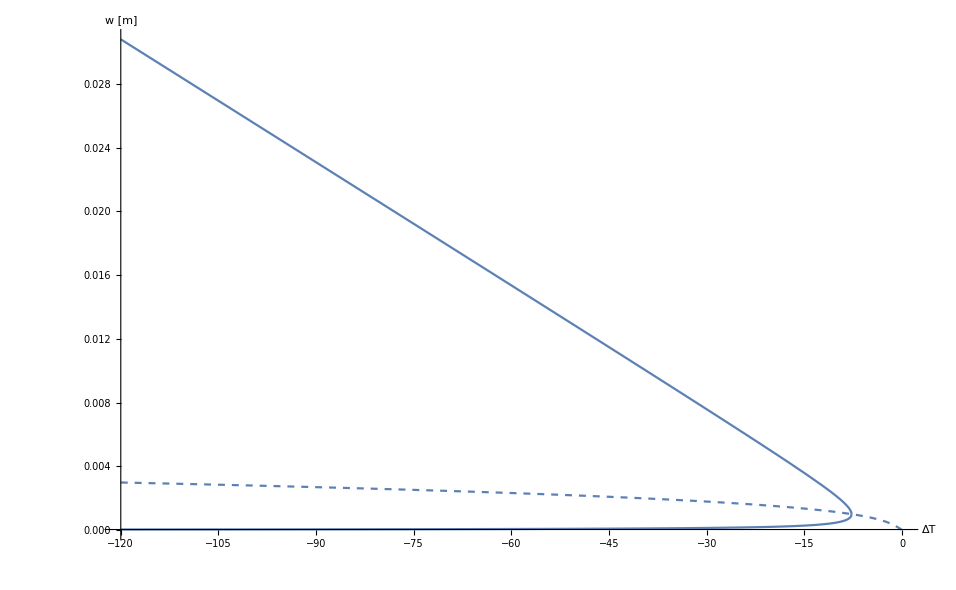

```mathematica
Show [p1x,p2x,p3x,Axes-> {True,True},AxesLabel->{"ΔT","w [m]"}]
```